#### Experimental Test of the Double Cover: Ramsey–Berry Interferometric Protocol

In SU(2), a rotation around z corresponds to ⅇ^(-ⅈ Ω/2 σ_z). This implies ⅇ^(-ⅈ (2π)/2 σ_z)=-𝕀 while ⅇ^(-ⅈ (4π)/2 σ_z)=𝕀.

```mathematica
MatrixForm[MatrixExp[-ⅈ #/2 PauliMatrix[3]]]&/@{2π,4π}
```

{(-1 | 0
0 | -1),(1 | 0
0 | 1)}

On the other hand, in SO(3) the z-rotation by the angle 2π reproduces identify:

```mathematica
RotationMatrix[2π,{0,0,1}]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

That’s the double-cover statement.

Consider a sequence of pulses as X_(π/2)->Z_γ->X_(-π/2) which corresponds to textbook Ramsey interferometer. Assuming a qubit is prepared in an initial state 0, the final state vector after this sequence of pulses given by:

```mathematica
FullSimplify@Fold[#2.#1&,{1,0},{MatrixExp[-ⅈ(π/2)/2 PauliMatrix[1]],MatrixExp[-ⅈ γ/2 PauliMatrix[3]],MatrixExp[-ⅈ(-π/2)/2 PauliMatrix[1]]}]
```

{Cos[γ/2],Sin[γ/2]}

The above formula implies that the probability of observing 1 is P_1=sin^2(γ/2). So as a function of the SU(2) rotation angle γ, you will see a 2π periodic signal in single-qubit populations, as shown below.

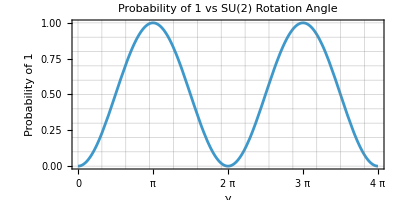

```mathematica
Plot[Sin[γ/2]^2,{γ,0,4π},PlotLabel->"Probability of 1 vs SU(2) Rotation Angle",AspectRatio->1/2,Frame->True,FrameLabel->{"γ", "Probability of 1"},FrameTicks->{Automatic, {Range[0,4π,π/2], None}},GridLines->All]
```

But the important and interesting part is not comparison with SU(2) rotation angle, but with an actual classical knob (a parameter describing the loop in control space). Ramsey reads out SU(2) phase, and that phase depends on the loop knob with a half-angle rule. That half-angle is the SU(2) vs SO(3) difference. With that experimental scenraio in place, we shall see a vislization as below, which shows that the population is 4π-periodic in the classical knob; That is the “double cover” fingerprint in a one-qubit interferometric readout: period doubling in the control-loop parameter, not in the SU(2) angle.

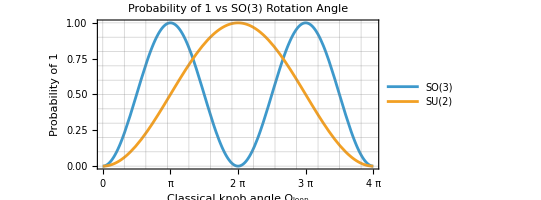

```mathematica
Plot[{Sin[γ/2]^2,Sin[γ/4]^2},{γ,0,4π},PlotLabel->"Probability of 1 vs SO(3) Rotation Angle",AspectRatio->1/2,Frame->True,FrameLabel->{"Classical knob angle Ω_loop", "Probability of 1"},FrameTicks->{Automatic, {Range[0,4π,π/2], None}},GridLines->All,PlotLegends->{"SO(3)","SU(2)"}]
```

But how to implement above Ramsey scenario? How can a one-qubit Ramsey interference produce a 4π-periodic signal in some classical loop knob, even though you can’t measure the global sign? The only way a single-qubit Ramsey experiment shows “4π vs 2π” is if the measured Ramsey phase γ depends on some classical loop knob Ω_loop as γ(Ω_loop)=Ω_loop/2, so that P_1=sin^2(Ω_loop/4) which is 4π periodic in Ω_loop.

Consider a classical, programmable loop such that the effective field seen by the qubit {Ω_x(t),Ω_y(t),Ω_z(t)} moves around and returns to where it started: {Ω_x(0),Ω_y(0),Ω_z(0)}={Ω_x(T),Ω_y(T),Ω_z(T)}. The waveforms {Ω_x(t),Ω_y(t),Ω_z(t)} is what you literally upload into an Arbitrary Waveform Generator (AWG). AWG is one of the main classical instruments that creates the time-dependent control signals you use to drive and shape qubit pulses eg in a transmon + circuit QED step.  The AWG generates two baseband waveforms: I(t) and Q(t). An IQ mixer combines them with the LO to produce a shaped microwave tone. So the AWG is your classical knob generator for: pulse amplitude A(t)=√((I(t))^2+(Q(t))^2), pulse phase φ(t)=arctan2(Q(t),I(t)), pulse timing and shape. In the rotating frame, a driven transmon qubit is often modeled as: H=1/2 Ω⃗(t).σ⃗ where the AWG controls (through the IQ mixer): Ω_x(t)∝I(t), Ω_y∝Q(t) and Ω_z is detuning (set by LO frequency choice and/or flux tuning). A classical loop of the control vector Ω(t) (AWG-programmed) is an SO(3)-type object (a 3-vector direction in ordinary space).

Let’s rephrase above ideas again. You program the AWG to generate waveforms I(t), Q(t), and together with LO settings (and possibly flux tuning) you realize a time-dependent effective drive vector: Ω⃗(t)={Ω_x(t),Ω_y(t),Ω_z(t)} . “Closed loop” means Ω⃗(0)=Ω⃗(T). So at the beginning and end you have the same Hamiltonian. From the classical control perspective you did one full cycle and came back. A concrete AWG prescription is a constant magnitude Ω where: 
Ω_x(t)=Ω sin θ cos ϕ(t)
Ω_y(t)=Ω sin θ sin ϕ(t)
Ω_z(t)=Ω cos θ 
with ϕ(t)=2π t/T.

Therefore, the Hamiltonian becomes H(t)=1/2 Ω n⃗(t).σ⃗ with n⃗(t)={sin θ cos ϕ(t),sin θ sin ϕ(t),cos θ}. So the direction of the effective field traces a cone at fixed polar angle θ, while the magnitude Ω stays constant. This is the loop Hamiltonian (H(0)=H(T)) that we will drive our qubit with.

```mathematica
Manipulate[Show[[{Sin[θ]Cos[2π tf],Sin[θ] Sin[2π tf],Cos[θ]},"ShowLabels"->False,ImageSize->Small],Graphics3D[{EdgeForm[Dashed],ColorData[97][2],Opacity[.2],Cone[{{0,0,Cos[θ]},{0,0,0}},Sin[θ]]}],ParametricPlot3D[{Sin[θ]Cos[2π t],Sin[θ] Sin[2π t],Cos[θ]},{t,0,tf}]],Item["n⃗(t)={sin θ cos ϕ(t),sin θ sin ϕ(t),cos θ}",Alignment->Center],{{θ,π/4,"Polar angle θ"},0,π},{{tf,10^-3,"Time t"},10^-3,1},SaveDefinitions->True]
```

Define the loop Hamiltonian H(t)=1/2 Ω n⃗(t).σ⃗ with n⃗(t)={sin θ cos ϕ(t),sin θ sin ϕ(t),cos θ} and ϕ(t)=2π t/T=ω t where ω=2π/T:

```mathematica
ClearAll[Ω,θ,T,Λ,t,ω];
$Assumptions=Ω>0&&ω>0&&θ∈Reals&&T>0&&Λ>0;
ham=FromSphericalCoordinates[{Ω,θ,ω t}].Table[PauliMatrix[j],{j,3}]/2//FullSimplify
```

{{1/2 Ω Cos[θ],1/2 ⅇ^(-ⅈ t ω) Ω Sin[θ]},{1/2 ⅇ^(ⅈ t ω) Ω Sin[θ],-1/2 Ω Cos[θ]}}

Solve dynamical equation for the corresponding unitary ⅈ ⅆU/ⅆt=H(t)U:

```mathematica
unitary=FullSimplify[DSolveValue[{ⅈ D[u[t],t]==ham.u[t],u[0]==IdentityMatrix[2]},u[t]∈Matrices[{2,2}],t]]
```

{{ⅇ^(-1/2 ⅈ t ω) (Cosh[1/2 t √(-ω^2-Ω^2+2 ω Ω Cos[θ])]+(ⅈ (ω-Ω Cos[θ]) Sinh[1/2 t √(-ω^2-Ω^2+2 ω Ω Cos[θ])])/(√(-ω^2-Ω^2+2 ω Ω Cos[θ]))),-(ⅈ ⅇ^(-1/2 ⅈ t ω) Ω Sin[θ] Sinh[1/2 t √(-ω^2-Ω^2+2 ω Ω Cos[θ])])/(√(-ω^2-Ω^2+2 ω Ω Cos[θ]))},{-(ⅈ ⅇ^((ⅈ t ω)/2) Ω Sin[θ] Sinh[1/2 t √(-ω^2-Ω^2+2 ω Ω Cos[θ])])/(√(-ω^2-Ω^2+2 ω Ω Cos[θ])),ⅇ^((ⅈ t ω)/2) (Cosh[1/2 t √(-ω^2-Ω^2+2 ω Ω Cos[θ])]-(ⅈ (ω-Ω Cos[θ]) Sinh[1/2 t √(-ω^2-Ω^2+2 ω Ω Cos[θ])])/(√(-ω^2-Ω^2+2 ω Ω Cos[θ])))}}

Cross-check that unitary satisfies its dynamical equation and also the initial condition:

```mathematica
FullSimplify[I D[unitary,t]-ham.unitary] =={{0,0},{0,0}} 
FullSimplify[unitary/. t->0] ==IdentityMatrix[2]
```

True

True

In the formula of the unitary operator U(t), replace √(ω^2+Ω^2-2ω Ω cos θ) by Λ, for simplicity of formulas:

```mathematica
unitary=unitary/.{√(-ω^2-Ω^2+2 ω Ω Cos[θ]):>ⅈ Λ,1/(√(-ω^2-Ω^2+2 ω Ω Cos[θ])):>1/(ⅈ Λ)}//FullSimplify
```

{{ⅇ^(-1/2 ⅈ t ω) (Cos[(t Λ)/2]+(ⅈ (ω-Ω Cos[θ]) Sin[(t Λ)/2])/Λ),-(ⅈ ⅇ^(-1/2 ⅈ t ω) Ω Sin[θ] Sin[(t Λ)/2])/Λ},{-(ⅈ ⅇ^((ⅈ t ω)/2) Ω Sin[θ] Sin[(t Λ)/2])/Λ,ⅇ^((ⅈ t ω)/2) (Cos[(t Λ)/2]-(ⅈ (ω-Ω Cos[θ]) Sin[(t Λ)/2])/Λ)}}

Cross-check that the unitary operator is the same as U(t)=ⅇ^(-ⅈ (ω t)/2 σ_z)ⅇ^(-ⅈ t/2(Ω sin θ σ_x + (Ω cos θ -ω)σ_z)):

```mathematica
FullSimplify[MatrixExp[-ⅈ ω t/2PauliMatrix[3]].MatrixExp[-ⅈ t/2(Ω Sin[θ]PauliMatrix[1]+(Ω Cos[θ]-ω)PauliMatrix[3])]/.{√(ω^2+Ω^2-2 ω Ω Cos[θ]):> Λ,1/(√(ω^2+Ω^2-2 ω Ω Cos[θ])):>1/Λ}]-unitary//FullSimplify
```

{{0,0},{0,0}}

After one loop (t=T), the first term ⅇ^(-ⅈ (ω t)/2 σ_z) in the unitary operator U(T) becomes -𝕀:

```mathematica
MatrixExp[-ⅈ (ω t)/2 PauliMatrix[3]]/.{ω->2π/T,t->T}
```

{{-1,0},{0,-1}}

The second term  ⅇ^(-ⅈ T/2(Ω sin θ σ_x + (Ω cos θ -ω)σ_z)) in the unitary operator U(T) is a rotation about the fixed axis m⃗=1/Λ{Ω sin θ,0,Ω cos θ-ω} by angle Λ T. 
Cross-check the above statement:

```mathematica
MatrixExp[-ⅈ T/2(Ω Sin[θ]PauliMatrix[1]+(Ω Cos[θ]-ω)PauliMatrix[3])]-With[{Λ=√(Ω^2+ω^2-2Ω ω Cos[θ])},{m={Ω Sin[θ],0,Ω Cos[θ]-ω}/Λ,σ=Table[PauliMatrix[j],{j,3}]},MatrixExp[-ⅈ T Λ/2 m.σ]]
```

{{0,0},{0,0}}

Cross-check that  m⃗=1/Λ{Ω sin θ,0,Ω cos θ-ω} is a unit vector:

```mathematica
FullSimplify@With[{Λ=√(Ω^2+ω^2-2Ω ω Cos[θ])},{m={Ω Sin[θ],0,Ω Cos[θ]-ω}/Λ},m.m]
```

1

Now we shall decompose the second term of U(T) into Euler angles to represent it as sequence of YZY pulses. The main motivation here is to explore how U(T) can be practically becomes a z-pulse.

Calculate the rotation matrix transforming the unit vector m⃗ into the unit vector along z-axis {0,0,1}:

```mathematica
FullSimplify@With[{Λ=√(Ω^2+ω^2-2Ω ω Cos[θ])},{m={Ω Sin[θ],0,Ω Cos[θ]-ω}/Λ},RotationMatrix[{m,{0,0,1}}]]//MatrixForm
```

((-ω+Ω Cos[θ])/(√(ω^2+Ω^2-2 ω Ω Cos[θ])) | 0 | -(Ω Sin[θ])/(√(ω^2+Ω^2-2 ω Ω Cos[θ]))
0 | 1 | 0
(Ω Sin[θ])/(√(ω^2+Ω^2-2 ω Ω Cos[θ])) | 0 | (-ω+Ω Cos[θ])/(√(ω^2+Ω^2-2 ω Ω Cos[θ])))

As you may have recognized, this is a rotation around y by an angle:

```mathematica
MatrixForm@RotationMatrix[-β,{0,1,0}]
```

(Cos[β] | 0 | -Sin[β]
0 | 1 | 0
Sin[β] | 0 | Cos[β])

where tan β=(Ω sin θ)/(Ω cos θ -ω). In other words, one can rotate U(T) along y-axis with a properly chosen angle such that the result becomes a z-pulse. The axis-alignment pulses ensure the loop contributes only a phase rotation about z in the lab basis.  In other words, the unitary operator U(T) can be written as U(T)=-𝕀 Y_β Z_γ Y_-β where γ=Λ T and tan β=(Ω sin θ)/(Ω cos θ -ω). Of course having -𝕀 is redundant in this formula, but we include it there for clarity.

So, ignoring -𝕀 factor (which is not observable for 1-qubit scenarios, but one can see its effect for 2-qubit cases which are beyond our scope for now), the one-loop unitary can be written as U(T)=Y_β Z_γ Y_-β. So if one designs sequence pulses as X_(π/2)->Y_β->U(T)->Y_-β->X_(-π/2), with properly chosen β, the sequence would be effectively X_(π/2)->Z_γ->X_(-π/2). We have shown that this seqeunce gives the proabbiltity of 1 as P_1=sin^2(γ/2). Pluggin γ=Λ T gives P_1=sin^2(T/2 √(Ω^2+(4 π^2)/T^2-(4π)/T Ω cos θ))

The Ramsey–Berry protocol uses a qubit as a built-in two-path interferometer. A π/2 pulse creates a superposition, then an adiabatic parameter sweep traces a closed loop on the Bloch sphere, accumulating a geometric (Berry) phase. A second π/2 pulse converts this phase into a measurable population difference.